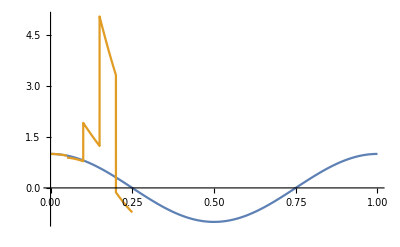

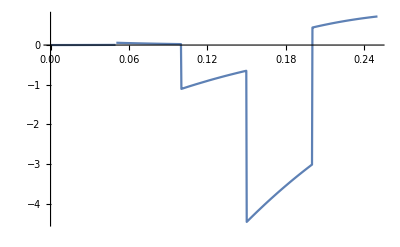

```mathematica
(* f(t) = E^(-t) с интерполационни възли x[k] = k / n, k = 0,1,.......,n *)
n=20;
Do[x[k]=k/n,{k,0,n}];
f[t_]:= Cos[2*Pi*t];

(* Тъй като възлите са равноотдалечени, то Δi = Xi+1 - Xi е едно и също число, а именно 1/n *)
delta=1/n;

(* Sn(x) се нарича пълна кубична интерполанта при този избор на d[0] и d[n] *)
d[0]=f'[x[0]];
d[n]=f'[x[n]];


(* Дефинираме коефициентите в тридиагоналната матрица *)
a=1/delta;
b=4/delta;
c=1/delta;

(* Дефинираме десните страни на уравненията в тридиагоналната матрица *)
Do[r[i]=3*((f[x[i]]-f[x[i-1]])/(delta^2)+(f[x[i+1]]-f[x[i]])/(delta^2)),{i,1,n-1}];

(* Начална инициализация на α1 и β1 *)
alpha[1]=-c/b;
beta[1]=r[1]/b;

(* Метод на прогонката - прав ход *)
Do[{alpha[k]=-c/(a*alpha[k-1]+b),beta[k]=(r[k]-a*beta[k-1])/(a*alpha[k-1]+b)},{k,2,n-1}];

(* Метод на прогонката - обратен ход *)
Do[d[k]=alpha[k]*d[k+1]+beta[k],{k,n-1,1,-1}];

(*общ вид на полиномите интерполиращи f(t) във всеки подинтервал на[0,1],определен от два последователни интерполационни възела*)
Do[sp[k,z_]=a[k]*(z-x[k])^2*(z-x[k+1])+b[k]*(z-x[k])^2+c[k]*(z-x[k])+d[k],{k,0,n-1}];

rec[i_,t_]:=If[i<=n+1,If[t>=x[i]&&t<x[i+1],sp[i,t],rec[i+1,t]]];
Sn[t_]:=rec[0,t];

Plot[{f[t],Sn[t]},{t,0,1},PlotPoints-> 300] (* Едновременно визуализиране на графиките на f[t] и Sn[t] в интервала [0,1] *)
Plot[f[t]-Sn[t],{t,0,1},PlotRange->All] (* Визуализиране на графиката на f[t] - Sn[t] в интервала [0,1] *)
```